```mathematica
Clear["Global`*"]
```

```mathematica
V = Log[(b + (x^2+ (b-y)^2)^(1/2) -y)/(a + (x^2+ (a-y)^2)^(1/2)-y)]
V2 = Integrate[1/Sqrt[x^2+ (y-c)^2],{c,a,b},Assumptions -> {a<b,b>0,y>0,x>0}]
```

```mathematica
Subscript[E, x]= FullSimplify[D[V,x]]
```

```mathematica
ExpandAll[(a/(√(x^2+(a-y)^2))-b/(√(x^2+(b-y)^2))+(-1/(√(x^2+(a-y)^2))+1/(√(x^2+(b-y)^2))) y)/x]
```

a/(x √(a^2+x^2-2 a y+y^2))-y/(x √(a^2+x^2-2 a y+y^2))-b/(x √(b^2+x^2-2 b y+y^2))+y/(x √(b^2+x^2-2 b y+y^2))

```mathematica
ExpandAll[(a/(√(x^2+(a-y)^2))-b/(√(x^2+(b-y)^2))-y/(√(x^2+(a-y)^2))+y/(√(x^2+(b-y)^2)))/x] ===ExpandAll[((a-y)/(√(x^2+(a-y)^2))+(y-b)/(√(x^2+(b-y)^2)))/x]
```

True

```mathematica
Subscript[E, y] = FullSimplify[Expand[D[V,y]]]
```

1/(√(x^2+(a-y)^2))-1/(√(x^2+(b-y)^2))

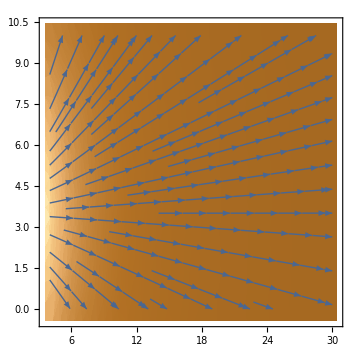

```mathematica
StreamDensityPlot[{-Subscript[E, x],-Subscript[E, y]},{x,4,30},{y,0,10}]
```

```mathematica
Integrate[Exp[ⅈ*k*r*Cos[θ-ϕ]],{θ,0,2π}]
```

```mathematica
ConditionalExpression[2 π BesselJ[0,k r],k r∈Reals]

ρ[x_,y_] := ( (x^2 + y^2)/(x^2 +y^2+ a^2))* ( (x^2 + (y-d)^2)/(x^2 +(y-d)^2+ a^2))
```

ConditionalExpression[2 π BesselJ[0,k r],k r∈Reals]

```mathematica
Plot3D[ρ[x,y],{x,-20,20},{y,-20,20},PlotPoints -> 100,PlotRange -> {0,1}]
```

-Graphics3D-

```mathematica
v[x_,y_] := (1/(x^2+y^2)+1/(x^2+(y-20)^2) - 2/Sqrt[(x^2+y^2)(x^2+(y-20)^2)]  )
```

```mathematica
Plot3D[ρ[x,y]*v[x,y],{x,-30,30},{y,-30,30},PlotPoints-> 100,PlotRange -> {-0.1,0.1}]
```

-Graphics3D-

$Aborted

$Aborted

```mathematica
Integrate[r/(r^2+a^2),{r,0,R}]
```

$Aborted